# Fig. 4: MPACS Postselection Statistics

## 1. Fixed Parameters

```mathematica
ClearAll[ "Global`*"];
```

```mathematica
nRaw = 10000;
```

```mathematica
nMeasValues = {50, 100, 400, 500};
```

```mathematica
t = N[ Pi/50];
```

```mathematica
deltaPhi = N[ Pi/2];
```

```mathematica
alpha = 1.0;
```

```mathematica
varphi = N[ Pi/2];
```

```mathematica
mCatValues = {0, 1, 2};
```

```mathematica
catDim = 60;
```

```mathematica
dynDim = 3;
```

```mathematica
seed = 1;
```

```mathematica
fontBase = 26;
```

```mathematica
fontPanel = 34;
```

```mathematica
fontNMeas = 25;
```

```mathematica
fontLegend = 27;
```

## 2. Coherent and Photon-Added Cat States

```mathematica
coherentState[ beta_, dim_Integer] := Module[ {nn, psi}, nn = Range[ 0, dim - 1]; psi = N[ Exp[ -Abs[ beta]^2/2]*beta^nn/Sqrt[ N[ Factorial[ nn]]]]; psi/Norm[ psi] ];
```

```mathematica
applyCreation[ psi_List] := Prepend[ Sqrt[ N[ Range[ Length[ psi] - 1]]]*Most[ psi], 0. + 0. I];
```

```mathematica
mpacsState[ amp_, phase_, mCat_Integer, dim_Integer] := Module[ {psi}, psi = coherentState[ amp, dim] + Exp[ I*phase]*coherentState[ -amp, dim]; psi = Nest[ applyCreation, psi, mCat]; psi/Norm[ psi] ];
```

## 3. Truncated States, Kraus Operators, and Weak Values

```mathematica
psiFFull = Association@Table[ mCat -> mpacsState[ alpha, varphi, mCat, catDim], {mCat, mCatValues}];
```

```mathematica
psiF = Association@Table[ mCat -> Take[ psiFFull[ mCat], dynDim], {mCat, mCatValues}];
```

```mathematica
psiI = ConstantArray[ 1./Sqrt[ dynDim] + 0. I, dynDim];
```

```mathematica
n = N[ Range[ 0, dynDim - 1]];
```

```mathematica
aOp = DiagonalMatrix[ n];
```

```mathematica
mPlus = (Exp[ -I*t*n] - Exp[ I*deltaPhi]*Exp[ I*t*n])/2;
```

```mathematica
mMinus = (Exp[ -I*t*n] + Exp[ I*deltaPhi]*Exp[ I*t*n])/2;
```

```mathematica
weakValues = Association@Table[  mCat -> (Conjugate[ psiF[ mCat]].(aOp.psiI))/(Conjugate[ psiF[ mCat]].psiI), {mCat, mCatValues}];
```

```mathematica
Do[ Print[ "m_cat=", mCat, ": A_w=", weakValues[ mCat]], {mCat, mCatValues}];
```

m_cat=0: A_w=0.87226+0.0748281 ⅈ

m_cat=1: A_w=1.66667+0.471405 ⅈ

m_cat=2: A_w=2.+0. ⅈ

## 4. NumPy-Compatible Random Numbers

```mathematica
numpySeedWords[ seed_Integer /; seed >= 0] := Module[  {entropy, pool = ConstantArray[ 0, 4], hc = 16^^43b0d7e5, hashmix, mix, words, v}, entropy = Reverse[ IntegerDigits[ seed, 2^32]]; hashmix[ value_] := Module[ {z = BitXor[ value, hc]}, hc = Mod[ hc*16^^931e8875, 2^32]; z = Mod[ z*hc, 2^32]; BitXor[ z, BitShiftRight[ z, 16]]]; mix[ x_, y_] := Module[ {z = Mod[ 16^^ca01f9dd*x - 16^^4973f715*y, 2^32]}, BitXor[ z, BitShiftRight[ z, 16]]]; Do[ pool[ [ j]] = hashmix[ If[ j <= Length[ entropy], entropy[ [ j]], 0]], {j, 4}]; Do[ If[ j != k, pool[ [ k]] = mix[ pool[ [ k]], hashmix[ pool[ [ j]]]]], {j, 4}, {k, 4}]; Do[ pool[ [ k]] = mix[ pool[ [ k]], hashmix[ entropy[ [ j]]]], {j, 5, Length[ entropy]}, {k, 4}]; hc = 16^^8b51f9dd; words = Table[  v = BitXor[ pool[ [ Mod[ j - 1, 4] + 1]], hc]; hc = Mod[ hc*16^^58f38ded, 2^32]; v = Mod[ v*hc, 2^32]; BitXor[ v, BitShiftRight[ v, 16]], {j, 8}]; (#[ [ 1]] + 2^32*#[ [ 2]] &) /@ Partition[ words, 2] ];
```

```mathematica
pcgMultiplier = 47026247687942121848144207491837523525;
```

```mathematica
pcgBatchCoefficients[ count_Integer] := pcgBatchCoefficients[ count] = { Rest[ NestList[ Mod[ pcgMultiplier*#, 2^128] &, 1, count]], Rest[ NestList[ Mod[ pcgMultiplier*# + 1, 2^128] &, 0, count]]};
```

```mathematica
initializePCG64[ seed_Integer /; seed >= 0] := Module[ {words, initialState, initialSequence}, words = numpySeedWords[ seed]; initialState = words[ [ 1]]*2^64 + words[ [ 2]]; initialSequence = words[ [ 3]]*2^64 + words[ [ 4]]; pcgIncrement = Mod[ 2*initialSequence + 1, 2^128]; pcgState = Mod[ pcgMultiplier*Mod[ pcgIncrement + initialState, 2^128] + pcgIncrement, 2^128]; ];
```

```mathematica
numpyRandom[ count_Integer?Positive] := Module[ {coef, states, values, rotations, bits}, coef = pcgBatchCoefficients[ count]; states = Mod[ coef[ [ 1]]*pcgState + coef[ [ 2]]*pcgIncrement, 2^128]; pcgState = Last[ states]; values = BitXor[ BitShiftRight[ states, 64], Mod[ states, 2^64]]; rotations = BitShiftRight[ states, 122]; bits = BitOr[ BitShiftRight[ values, rotations], Mod[ BitShiftLeft[ values, Mod[ -rotations, 64]], 2^64]]; N[ BitShiftRight[ bits, 11]]/2.^53 ];
```

## 5. Sequential Measurement and Postselection

```mathematica
simulateAll[ ] := Module[  {psi, q, rawData = <||>, postData, plus, minus, pPlus, pMinus, choosePlus, norm, xx, pf, keep}, initializePCG64[ seed]; psi = ConstantArray[ psiI, nRaw]; q = ConstantArray[ 0, nRaw]; postData = Association@Table[ mCat -> <||>, {mCat, mCatValues}]; Do[  plus = Transpose[ mPlus*Transpose[ psi]]; minus = Transpose[ mMinus*Transpose[ psi]]; pPlus = Re[ Total[ Abs[ plus]^2, {2}]]; pMinus = Re[ Total[ Abs[ minus]^2, {2}]]; choosePlus = MapThread[ Boole[ #1 < #2] &, {numpyRandom[ nRaw], Clip[ pPlus, {0., 1.}]}]; norm = Sqrt[ choosePlus*pPlus + (1 - choosePlus)*pMinus]; psi = (choosePlus*plus + (1 - choosePlus)*minus)/norm; q += choosePlus; If[ MemberQ[ nMeasValues, step], xx = N[ q/step] - 0.5; AssociateTo[ rawData, step -> xx]; Do[  pf = Clip[ Abs[ psi.Conjugate[ psiF[ mCat]]]^2, {0., 1.}]; keep = MapThread[ Less, {numpyRandom[ nRaw], pf}]; AssociateTo[ postData, mCat -> Append[ postData[ mCat], step -> Pick[ xx, keep, True]]], {mCat, mCatValues}] ], {step, 1, Last[ nMeasValues]}]; {rawData, postData} ];
```

## 6. Histogram Heights and Gaussian Smoothing

```mathematica
heights[ xx_List, nMeas_Integer] := Module[ {q, counts}, q = Round[ (xx + 0.5)*nMeas]; counts = Counts[ q]; N[ Lookup[ counts, Range[ 0, nMeas], 0]/nMeas] ];
```

```mathematica
smoothKernel[ nMeas_Integer, xCurve_List, sigmaBins_] := Module[ {x}, x = N[ Range[ 0, nMeas]/nMeas] - 0.5; Exp[ -0.5*(Outer[ Subtract, xCurve, x]*nMeas/sigmaBins)^2]/(Sqrt[ 2.*Pi]*sigmaBins) ];
```

## 7. Run the Simulation

```mathematica
{raw, post} = simulateAll[ ];
```

## 8. Colors, Line Styles, and Layout

```mathematica
hexColor[ s_String] := RGBColor @@ (IntegerDigits[ FromDigits[ StringDrop[ s, 1], 16], 256, 3]/255.);
```

```mathematica
fills = <|"raw" -> hexColor[ "#97CFDA"], 0 -> hexColor[ "#ECCFA4"], 1 -> hexColor[ "#E69FA9"], 2 -> hexColor[ "#A9D0AF"]|>;
```

```mathematica
meanColors = <|"raw" -> hexColor[ "#5AAFC0"], 0 -> hexColor[ "#D1A968"], 1 -> hexColor[ "#C96C7E"], 2 -> hexColor[ "#73B183"]|>;
```

```mathematica
curveStyles = <|"raw" -> {}, 0 -> 1.35*{5., 3.}, 1 -> 1.35*{0.8, 2.0}, 2 -> 1.35*{5., 2., 1., 2.}|>;
```

```mathematica
widths = <|0 -> 0.98, 1 -> 0.84, 2 -> 0.70|>;
```

```mathematica
panelScale = {1.15, 1.10, 1.05, 1.00};
```

```mathematica
panelLabels = {"(a)", "(b)", "(c)", "(d)"};
```

```mathematica
groupKeys = {"raw", 0, 1, 2};
```

```mathematica
figureWidth = 9.2*72;
```

```mathematica
figureHeight = 7.*72;
```

```mathematica
leftMargin = 0.025;
```

```mathematica
rightMargin = 0.995;
```

```mathematica
bottomMargin = 0.03;
```

```mathematica
topMargin = 0.85;
```

```mathematica
panelWidth = (rightMargin - leftMargin)*figureWidth/(2 + 0.04);
```

```mathematica
panelHeight = (topMargin - bottomMargin)*figureHeight/(2 + 0.12);
```

## 9. Histogram Panels and Mean Lines

```mathematica
makePanel[ index_Integer, nMeas_Integer] := Module[  {groups, x, hh, rawBars, catBars, order, sigmaBins, xCurve, kernel, yy, curveLines, meanLines, yMax, label, meanX}, groups = Join[ <|"raw" -> raw[ nMeas]|>, Association@Table[ mCat -> post[ mCat][ nMeas], {mCat, mCatValues}]]; x = N[ Range[ 0, nMeas]/nMeas] - 0.5; hh = Association@Table[ key -> heights[ groups[ key], nMeas], {key, groupKeys}]; rawBars = {fills[ "raw"], EdgeForm[ {Black, AbsoluteThickness[ Min[ 0.35, 35./nMeas]]}], Table[ Rectangle[ {x[ [ j]] - 0.5/nMeas, 0}, {x[ [ j]] + 0.5/nMeas, hh[ "raw"][ [ j]]}], {j, nMeas + 1}]}; order = Flatten[ Table[ With[ {rank = Reverse[ SortBy[ mCatValues, {hh[ #][ [ j]], #} &]]}, Table[ {level, rank[ [ level]], j}, {level, Length[ mCatValues]}]], {j, nMeas + 1}], 1]; catBars = Table[ With[ {mCat = item[ [ 2]], j = item[ [ 3]]}, {fills[ mCat], Opacity[ 0.9], EdgeForm[ {Black, Opacity[ 0.9], AbsoluteThickness[ Min[ 0.30, 30./nMeas]]}], Rectangle[ {x[ [ j]] - widths[ mCat]*panelScale[ [ index]]/(2*nMeas), 0}, {x[ [ j]] + widths[ mCat]*panelScale[ [ index]]/(2*nMeas), hh[ mCat][ [ j]]}]}], {item, SortBy[ order, {#[ [ 1]] &, #[ [ 2]] &, #[ [ 3]] &}]}]; sigmaBins = If[ nMeas <= 100, 1., 3.5]; xCurve = Subdivide[ First[ x], Last[ x], 12*nMeas]; kernel = smoothKernel[ nMeas, xCurve, sigmaBins]; yy = Association@Table[ key -> kernel.hh[ key], {key, groupKeys}]; yMax = 1.05*Max[ Flatten[ Values[ hh]], Flatten[ Values[ yy]]]; curveLines = Table[  {Black, AbsoluteThickness[ 1.35], AbsoluteDashing[ curveStyles[ key]], Line /@ Select[ SplitBy[ Transpose[ {xCurve, yy[ key]}], Last[ #] > 10^-8 &], Length[ #] >= 2 && Last[ First[ #]] > 10^-8 &]}, {key, groupKeys}]; meanLines = Table[ If[ Length[ groups[ key]] > 0, meanX = Mean[ groups[ key]]; {meanColors[ key], AbsoluteThickness[ 2.4], AbsoluteDashing[ 2.4*{4., 2.4}], Line[ {{meanX, 0}, {meanX, yMax}}]}, {}], {key, groupKeys}]; label = Style[ Row[ {Subscript[ Style[ "N", Italic], Style[ "m", Plain]], " = ", nMeas}], FontFamily -> "Times", FontSize -> fontNMeas]; Graphics[ {rawBars, catBars, curveLines, meanLines, {Black, AbsoluteThickness[ 1.], Line[ {{-0.30, 0}, {0.30, 0}}]}, Inset[ Style[ panelLabels[ [ index]], Bold, FontFamily -> "Arial", FontSize -> fontPanel], Scaled[ {0.035, 0.94}], {-1, 1}], Inset[ label, Scaled[ {0.045, 0.70}], {-1, 1}]}, PlotRange -> {{-0.30, 0.30}, {0., yMax}}, PlotRangePadding -> None, PlotRangeClipping -> True, ImagePadding -> 0, AspectRatio -> panelHeight/panelWidth, ImageSize -> {panelWidth, panelHeight}, Background -> White, BaseStyle -> {FontFamily -> "Arial", FontSize -> fontBase}] ];
```

## 10. Assemble the Four Panels and Legend

```mathematica
panels = MapIndexed[ makePanel[ First[ #2], #1] &, nMeasValues];
```

```mathematica
legendLabels = {"No postselection", Row[ {Style[ "m", Italic], " = 0"}], Row[ {Style[ "m", Italic], " = 1"}], Row[ {Style[ "m", Italic], " = 2"}]};
```

```mathematica
legendText = Table[ Style[ legendLabels[ [ j]], FontFamily -> If[ j == 1, "Arial", "Times"], FontSize -> fontLegend], {j, 4}];
```

```mathematica
legendTextWidths = Table[ First[ ImageDimensions[  Rasterize[ legendText[ [ j]], "Image", ImageResolution -> 72]]], {j, 4}];
```

```mathematica
legendItemWidths = (1.25 + 0.45)*fontLegend + legendTextWidths;
```

```mathematica
legendStarts = Most[ FoldList[ Plus, 0, legendItemWidths + 1.6*fontLegend]];
```

```mathematica
legendWidth = Total[ legendItemWidths] + 3*1.6*fontLegend;
```

```mathematica
legend = Graphics[ Table[ { {EdgeForm[ {Black, AbsoluteThickness[ 0.7]}], fills[ groupKeys[ [ j]]], Rectangle[ {legendStarts[ [ j]], -0.4*fontLegend}, {legendStarts[ [ j]] + 1.25*fontLegend, 0.4*fontLegend}]}, Inset[ legendText[ [ j]], {legendStarts[ [ j]] + 1.7*fontLegend, 0}, {Left, Center}]}, {j, 4}], PlotRange -> {{-1, legendWidth + 1}, {-0.7*fontLegend, 0.7*fontLegend}}, PlotRangePadding -> None, ImagePadding -> 0, ImageSize -> {legendWidth + 2, 1.4*fontLegend}, AspectRatio -> 1.4*fontLegend/(legendWidth + 2)];
```

```mathematica
fig = Graphics[ { Table[ Inset[ panels[ [ idx]], {leftMargin*figureWidth + Mod[ idx - 1, 2]*panelWidth*1.04, topMargin*figureHeight - Quotient[ idx - 1, 2]*panelHeight*1.12}, {Left, Top}, {panelWidth, panelHeight}], {idx, 4}], Inset[ legend, {0.5*figureWidth, 0.99*figureHeight - 0.5*fontLegend}, {Center, Top}]}, PlotRange -> {{Min[ 0, (figureWidth - legendWidth - 2)/2] - 6, Max[ figureWidth, (figureWidth + legendWidth + 2)/2] + 6}, {0, figureHeight}}, PlotRangePadding -> None, ImagePadding -> 0, ImageSize -> {Max[ figureWidth, legendWidth + 2] + 12, figureHeight}, AspectRatio -> figureHeight/(Max[ figureWidth, legendWidth + 2] + 12), Background -> White];
```

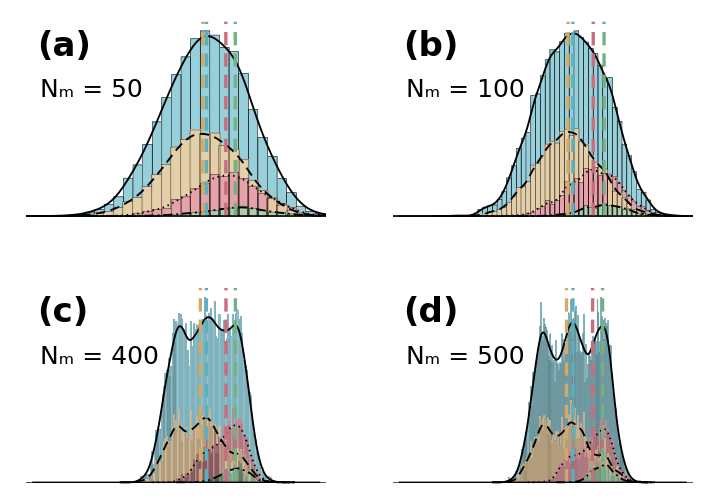

```mathematica
fig
```

## 11. Export PNG (Optional)

```mathematica
(*Export[ FileNameJoin[ {NotebookDirectory[ ], "Fig4_MPACS_Mathematica.png"}], ImagePad[ ImageCrop[ Rasterize[ fig, "Image", ImageResolution -> 600]], 60, White], "PNG", ImageResolution -> 600];*)
```